{5,4}

{6,19}

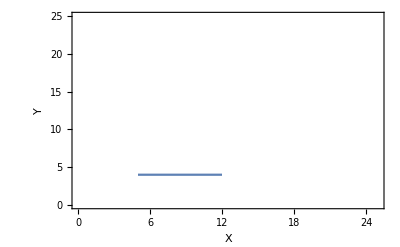

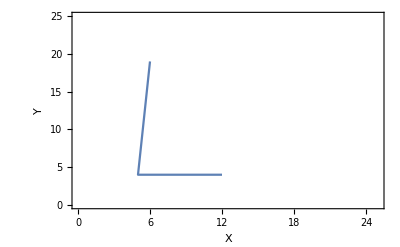

```mathematica
a=1;b=1;
P={12,4};q=23;
ki=Mod[(3*P[[1]]^2+a)*PowerMod[2 P[[2]],-1,q],q];
x4=Mod[ki^2-2 P[[1]],q];
y4=Mod[-ki (x4-P[[1]])-P[[2]],q];
S={x4,y4}
list4={P,S};
k5=Mod[(S[[2]]-P[[2]])*PowerMod[S[[1]]-P[[1]],-1,q],q];
x5=Mod[k5^2-P[[1]]-S[[1]],q];
y5=Mod[-k5(x5-P[[1]])-P[[2]],q];
T={x5,y5}
list5={P,S,T};
ListPlot[list4,Joined->True,PlotRange->{{0,25},{0,25}},PlotStyle->PointSize[0.02],Frame->True,FrameLabel->{X,Y}]
ListPlot[list5,Joined->True,PlotRange->{{0,25},{0,25}},PlotStyle->PointSize[0.02],Frame->True,FrameLabel->{X,Y}]
```

```mathematica
U[0]=S;
Do[k1=Mod[(U[n][[2]]-P[[2]])*PowerMod[U[n][[1]]-P[[1]],-1,q],q];
x1=Mod[k1^2-P[[1]]-U[n][[1]],q];
y1=Mod[-k1(x1-P[[1]])-P[[2]],q];
U[n+1]={x1,y1};,{n,0,30}]
```

PowerMod::ninv: 0 is not invertible modulo 23.

```mathematica
list1=Table[U[n],{n,0,11}]
```

{{5,4},{6,19},{17,20},{7,12},{13,16},{4,0},{13,7},{7,11},{17,3},{6,4},{5,19},{12,19}}

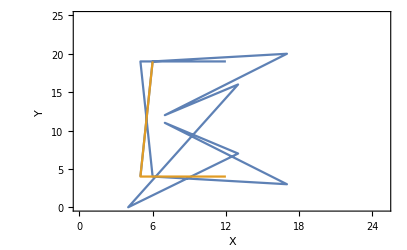

```mathematica
ListPlot[{list1,list5},Joined->True,PlotRange->{{0,25},{0,25}},PlotStyle->PointSize[0.02],Frame->True,FrameLabel->{X,Y}]
```

E_p(a,b)空间的模块化

## E_p(a,b)空间内的状态分布计算

### E_p(a,b)空间的模块化算法公式

#### ESpas[p,a,b]: ESpas代表E空间，p，a，b为各个参数

```mathematica
ESpas[p_,a_,b_]:=Module[{x,y,sdata={}},
For[x=0,x<p,x++,
For[y=0,y<p,y++,
If[Mod[y^2-x^3-a x-b,p]==0,sdata=Append[sdata,{x,y}]
]]];
sdata]
```

### 例1：E_23(1,1)空间的状态分布

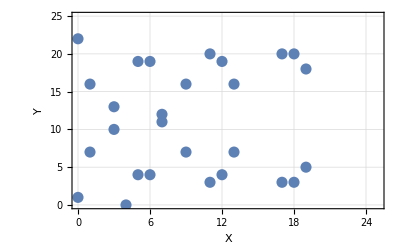

```mathematica
ListPlot[ESpas[23,1,1],PlotRange->{{0,25},{0,25}},PlotStyle->PointSize[0.02],Frame->True,GridLines->Automatic,FrameLabel->{X,Y}]
```

### 例2：E_291(4,20)空间的状态分布

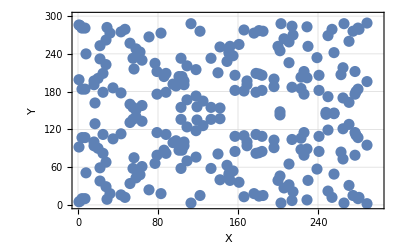

```mathematica
ListPlot[ESpas[291,4,20],PlotRange->{{0,300},{0,300}},PlotStyle->PointSize[0.02],Frame->True,GridLines->Automatic,FrameLabel->{X,Y}]
```

## E_p(a,b)空间内的状态顺序计算

### E_p(a,b)空间的模块化算法公式

```mathematica
EllipticSum[p_,a_,b_,P_,Q_]:=Module[{k,x,y,R},
Which[P=={},R=Q,
Q=={},R=P,
P[[1]]≠Q[[2]],
 k=Mod[(Q[[2]]-P[[2]])*PowerMod[Q[[1]]-P[[1]],-1,p],p];
x=Mod[k^2-P[[1]]-Q[[1]],p];
y=Mod[-k(x-P[[1]])-P[[2]],p];
R={x,y},
(P==Q)∧ (P≠{0}),
k=Mod[(3*P[[1]]^2+a)*PowerMod[2 P[[2]],-1,p],p];
x=Mod[k^2-2 P[[1]],p];
y=Mod[-k (x-P[[1]])-P[[2]],p];
R={x,y},
(P[[1]]==Q[[1]]) ∧ (P[[2]]≠Q[[2]]),R={0};
R]]
```

```mathematica
EllipticCont[n_,P_,p_,a_,b_]:=Module[{x,A,B},
x=n;A=P;B={O};
While[x>1,
If[OddQ[x],
B=EllipticSum[p,a,b,A,B];
x=x-1,
A=EllipticSum[p,a,b,A,A];
x=x/2;];
];
A=EllipticSum[p,a,b,A,B];
A]
```

```mathematica
G={12,4};p=23;
gr1=Table[EllipticCont[i,G,p,1,1],{i,1,27}]
```

PowerMod::pmod: The base and modulus arguments in PowerMod[0,-1.,23.] must be Gaussian integers and the power must be an integer or rational.

PowerMod::pmod: The base and modulus arguments in PowerMod[0.,-1.,23.] must be Gaussian integers and the power must be an integer or rational.

General::stop: Further output of PowerMod::pmod will be suppressed during this calculation.

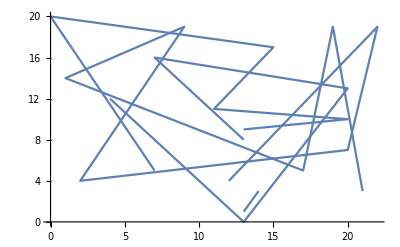

```mathematica
ListPlot[gr1,Joined->True]
```